# Final

#### Definitions

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
expA = "E2";
expB = "E2B";
```

```mathematica
dir2="E2B/45/";
```

```mathematica
cd=ColorData[97,"ColorList"];
```

```mathematica
fitness[e_,n_,t_]:=
Module[
{allevol,allfit,bestfit,bestindex,bestsorted},
allevol={};
allfit={};
bestfit  = {};
bestindex={};
For[i=0, i<n, i++,
evol = Transpose[Import[StringJoin[e,"/",ToString[i], "/fitness.dat"]]][[2]];
allevol=Append[allevol,evol];
fit=Last[evol];
allfit=Append[allfit,fit];
If[fit>t ,
bestfit = Append[bestfit,fit];
bestindex=Append[bestindex,i];
];
];
bestsorted = Sort[Transpose[{bestindex,bestfit}],#1[[2]]>#2[[2]]&];
{bestsorted,allevol,allfit}
]
```

## 1. Evolution

```mathematica
n=100;
t=0.5;
```

```mathematica
{bestsortedA,allevolA,allfitA} = fitness[expA,n,t];
{bestsortedB,allevolB,allfitB} = fitness[expB,n,t];
```

```mathematica
bestsortedA
bestsortedB
```

{{28,0.969962},{24,0.959654},{75,0.950725},{35,0.946028},{36,0.938188},{90,0.938174},{53,0.919681},{89,0.916205},{52,0.913958},{26,0.911635},{13,0.908978},{14,0.905421},{76,0.904914},{46,0.897533},{72,0.89367},{80,0.89305},{73,0.890718},{87,0.888238},{3,0.887545},{62,0.886786},{47,0.882246},{65,0.879521},{77,0.878666},{19,0.875196},{22,0.874576},{71,0.870183},{81,0.865338},{58,0.864318},{33,0.862847},{66,0.862473},{29,0.860522},{10,0.86032},{9,0.859233},{61,0.859057},{91,0.854253},{40,0.853335},{23,0.852453},{88,0.846561},{32,0.846305},{99,0.84447},{78,0.840356},{96,0.839467},{70,0.838151},{20,0.832687},{12,0.832617},{79,0.829451},{83,0.829294},{57,0.82736},{44,0.824611},{25,0.824426},{86,0.82396},{1,0.822824},{51,0.821711},{7,0.82169},{39,0.819917},{84,0.819835},{74,0.819555},{55,0.814768},{8,0.810391},{94,0.808381},{48,0.806503},{41,0.805123},{42,0.804921},{49,0.802186},{60,0.798034},{56,0.797788},{21,0.796755},{59,0.796314},{54,0.789348},{45,0.787952},{34,0.783979},{95,0.783969},{2,0.780648},{67,0.777216},{69,0.776306},{6,0.775518},{18,0.77199},{11,0.768776},{27,0.767324},{97,0.765751},{16,0.759002},{63,0.757626},{50,0.756166},{85,0.752541},{37,0.74923},{15,0.749175},{98,0.746286},{93,0.738652},{43,0.684069},{38,0.682114},{4,0.666957},{31,0.661983},{92,0.653901},{82,0.64829},{64,0.634544},{30,0.628347},{0,0.620705},{5,0.613646},{17,0.61182},{68,0.588741}}

{{76,0.990228},{96,0.989447},{45,0.981455},{31,0.969797},{88,0.957066},{49,0.955075},{15,0.954815},{2,0.951135},{8,0.949449},{29,0.946184},{48,0.941189},{74,0.939856},{23,0.939512},{78,0.938114},{98,0.926251},{59,0.923547},{80,0.920263},{87,0.919499},{51,0.91761},{37,0.917353},{33,0.917133},{28,0.914422},{73,0.914347},{7,0.910456},{66,0.907879},{91,0.906133},{99,0.904609},{26,0.899096},{50,0.896433},{60,0.893566},{61,0.887887},{13,0.886671},{46,0.885903},{70,0.885297},{62,0.884771},{22,0.880295},{0,0.880169},{85,0.876416},{89,0.876316},{63,0.873971},{41,0.87375},{92,0.872628},{27,0.871485},{56,0.867083},{24,0.864319},{58,0.860092},{36,0.858438},{11,0.857028},{43,0.856904},{72,0.8514},{52,0.850376},{79,0.849931},{34,0.849471},{64,0.849009},{71,0.847779},{90,0.846529},{94,0.844939},{86,0.844643},{10,0.841611},{69,0.839068},{4,0.837958},{30,0.829208},{5,0.828726},{68,0.82595},{25,0.824368},{1,0.824124},{12,0.824042},{19,0.821955},{77,0.821605},{65,0.816062},{57,0.811238},{18,0.809385},{32,0.809193},{93,0.80646},{82,0.806404},{14,0.805315},{20,0.800001},{40,0.796038},{55,0.795902},{67,0.793179},{17,0.784872},{39,0.784822},{6,0.7646},{97,0.751927},{84,0.749806},{44,0.749302},{38,0.735222},{75,0.734367},{81,0.724712},{16,0.722254},{42,0.714694},{3,0.712798},{95,0.702256},{53,0.691854},{9,0.689968},{35,0.676747},{47,0.645446},{54,0.639338},{21,0.611811},{83,0.609263}}

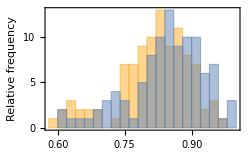

```mathematica
Histogram[{allfitA,allfitB},20,PlotRange->All,ImageSize->250,Frame->True,FrameLabel->{"Final fitness","Relative frequency"}]
```

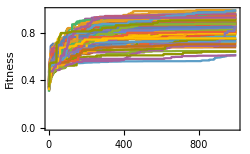

```mathematica
ListLinePlot[allevolB,Frame->True,FrameLabel->{"Generations","Fitness"},PlotRange->All,ImageSize->250]
```

## 2. Generalization

```mathematica
ab={};
perf={};
For[i=0, i<n, i++,
a = Flatten[Import[StringJoin[expB,"/",ToString[i], "/A_finalperf.dat"]]][[1]];
b =Flatten[Import[StringJoin[expB,"/",ToString[i], "/B_finalperf.dat"]]][[1]];
ab = Append[ab,{a,b}];
perf = Append[perf,a b];
];
```

```mathematica
perf
```

{0.8472,0.79644,0.911091,0.675997,0.778523,0.782442,0.739432,0.883329,0.917239,0.548034,0.788227,0.788571,0.776991,0.84803,0.785608,0.918328,0.657838,0.756731,0.778598,0.794023,0.756716,0.581631,0.844173,0.905185,0.821179,0.801825,0.835433,0.838822,0.879493,0.899725,0.779356,0.921556,0.743234,0.882907,0.819132,0.648463,0.80888,0.874695,0.700336,0.774413,0.727118,0.852356,0.68777,0.806923,0.727484,0.953616,0.835497,0.605678,0.876628,0.914806,0.866358,0.836144,0.784616,0.659165,0.634957,0.758276,0.822449,0.778622,0.819257,0.83484,0.868609,0.825874,0.849126,0.826187,0.815672,0.783988,0.840159,0.75784,0.777359,0.813314,0.833908,0.83319,0.780003,0.866302,0.904358,0.706856,0.945107,0.788144,0.90178,0.830807,0.886187,0.693351,0.756805,0.576531,0.715237,0.828666,0.803224,0.864035,0.910013,0.841338,0.819043,0.847243,0.839248,0.77438,0.811027,0.678044,0.951823,0.713924,0.8986,0.848159}

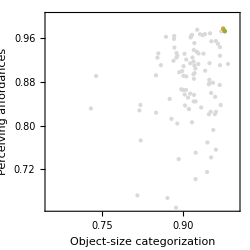

```mathematica
Show[
{
ListPlot[ab,PlotRange->{{0.65,1},{0.65,1}},Frame->True,PlotStyle->Directive[PointSize[Medium],LightGray],AspectRatio->1],
ListPlot[{ab[[46]]},PlotStyle->Directive[PointSize[Medium],cd[[2]]]],
ListPlot[{ab[[97]]},PlotStyle->Directive[PointSize[Medium],cd[[3]]]]
},
FrameLabel->{"Object-size categorization","Perceiving affordances"},ImageSize->250]
Export["individualperformance.eps",%];
```

```mathematica
perfindex = Transpose[{Table[x,{x,0,99}],perf}];
Sort[perfindex,#1[[2]]>#2[[2]]&]
```

{{45,0.953616},{96,0.951823},{76,0.945107},{31,0.921556},{15,0.918328},{8,0.917239},{49,0.914806},{2,0.911091},{88,0.910013},{23,0.905185},{74,0.904358},{78,0.90178},{29,0.899725},{98,0.8986},{80,0.886187},{7,0.883329},{33,0.882907},{28,0.879493},{48,0.876628},{37,0.874695},{60,0.868609},{50,0.866358},{73,0.866302},{87,0.864035},{41,0.852356},{62,0.849126},{99,0.848159},{13,0.84803},{91,0.847243},{0,0.8472},{22,0.844173},{89,0.841338},{66,0.840159},{92,0.839248},{27,0.838822},{51,0.836144},{46,0.835497},{26,0.835433},{59,0.83484},{70,0.833908},{71,0.83319},{79,0.830807},{85,0.828666},{63,0.826187},{61,0.825874},{56,0.822449},{24,0.821179},{58,0.819257},{34,0.819132},{90,0.819043},{64,0.815672},{69,0.813314},{94,0.811027},{36,0.80888},{43,0.806923},{86,0.803224},{25,0.801825},{1,0.79644},{19,0.794023},{11,0.788571},{10,0.788227},{77,0.788144},{14,0.785608},{52,0.784616},{65,0.783988},{5,0.782442},{72,0.780003},{30,0.779356},{57,0.778622},{18,0.778598},{4,0.778523},{68,0.777359},{12,0.776991},{39,0.774413},{93,0.77438},{55,0.758276},{67,0.75784},{82,0.756805},{17,0.756731},{20,0.756716},{32,0.743234},{6,0.739432},{44,0.727484},{40,0.727118},{84,0.715237},{97,0.713924},{75,0.706856},{38,0.700336},{81,0.693351},{42,0.68777},{95,0.678044},{3,0.675997},{53,0.659165},{16,0.657838},{35,0.648463},{54,0.634957},{47,0.605678},{21,0.581631},{83,0.576531},{9,0.548034}}

## 3. Connectome

```mathematica
iw2 =Import[StringJoin[dir2, "/interweights.dat"]];
```

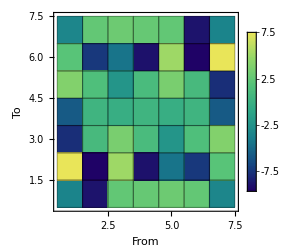

```mathematica
ListDensityPlot[iw2,InterpolationOrder->0,Mesh->All,ColorFunction->"BlueGreenYellow",PlotRange->{{0.5,7.5},{0.5,7.5},{-10,10}},Frame->True,FrameLabel->{"From","To"},ImageSize->250,PlotLegends->Automatic]
Export["f_weights.eps",%];
```

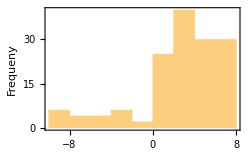

```mathematica
Histogram[Flatten[iw2],PlotRange->All,Frame->True,FrameLabel->{"Weight","Frequeny"},ImageSize->250]
Export["f_weightshist.eps",%];
```

```mathematica
Abs[Transpose[iw2][[3]]]
```

{3.60967,7.54601,7.87026,5.84081,3.9556,1.9996,3.40823,9.00148,9.68752,0.892969,0.330674,1.45569,7.4381,2.51551,2.4387,5.07792,3.52603,0.257025,2.36323,4.53281,2.96755,2.63221,9.08922,1.04336,0.304323,1.04336,9.08922,2.63221,2.96755,4.53281,2.36323,0.257025,3.52603,5.07792,2.4387,2.51551,7.4381,1.45569,0.330674,0.892969,9.68752,9.00148,3.40823,1.9996,3.9556,5.84081,7.87026,7.54601,3.60967}

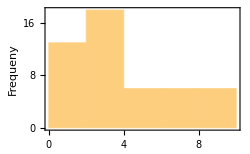

```mathematica
Histogram[Sort[Abs[Transpose[iw2][[3]]],#1<#2&],Frame->True,ImageSize->250,FrameLabel->{"Weight magnitude","Frequeny"}]
```

## 2. Behavior

### Task 1: Object Recognition

```mathematica
ba=Import[ StringJoin[dir2,"B_avoid_aposx.dat"]];
bc=Import[ StringJoin[dir2,"B_approach_aposx.dat"]];
```

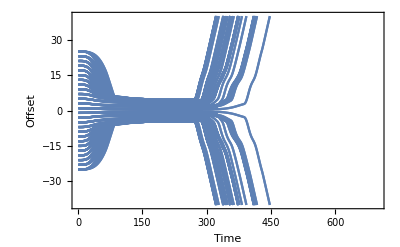

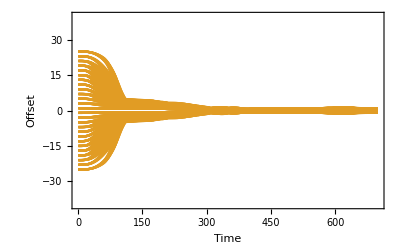

```mathematica
ListLinePlot[ba,PlotStyle->cd[[1]],PlotRange->{Automatic,{-40,40}},Frame->True,FrameLabel->{"Time","Offset"},ImageSize->400]
ListLinePlot[bc,PlotStyle->cd[[2]],PlotRange->{Automatic,{-40,40}},Frame->True,FrameLabel->{"Time","Offset"},ImageSize->400]
```

### Task 2: Perceiving Affordances

```mathematica
aa=Import[ StringJoin[dir2,"A_avoid_aposx.dat"]];
ac=Import[ StringJoin[dir2,"A_approach_aposx.dat"]];
```

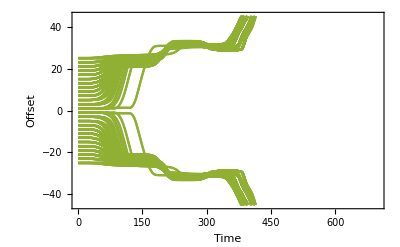

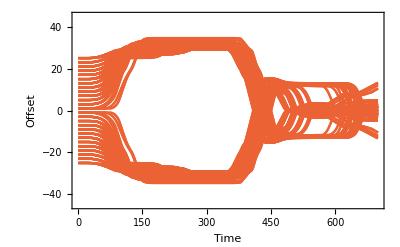

```mathematica
ListLinePlot[aa,PlotStyle->cd[[3]],PlotRange->{Automatic,{-45,45}},Frame->True,FrameLabel->{"Time","Offset"},ImageSize->400]
ListLinePlot[ac,PlotStyle->cd[[4]],PlotRange->{Automatic,{-45,45}},Frame->True,FrameLabel->{"Time","Offset"},ImageSize->400]
```

## X. Neural Activity

### Afford

#### Avoid

```mathematica
ba1=Import[StringJoin[dir2,"A_avoid_n1.dat"]];
ba2=Import[StringJoin[dir2,"A_avoid_n2.dat"]];
ba3=Import[StringJoin[dir2,"A_avoid_n3.dat"]];
ba4=Import[StringJoin[dir2,"A_avoid_n4.dat"]];
ba5=Import[StringJoin[dir2,"A_avoid_n5.dat"]];
ba6=Import[StringJoin[dir2,"A_avoid_n6.dat"]];
ba7=Import[StringJoin[dir2,"A_avoid_n7.dat"]];
```

#### Approach

```mathematica
bc1=Import[StringJoin[dir2,"A_approach_n1.dat"]];
bc2=Import[StringJoin[dir2,"A_approach_n2.dat"]];
bc3=Import[StringJoin[dir2,"A_approach_n3.dat"]];
bc4=Import[StringJoin[dir2,"A_approach_n4.dat"]];
bc5=Import[StringJoin[dir2,"A_approach_n5.dat"]];
bc6=Import[StringJoin[dir2,"A_approach_n6.dat"]];
bc7=Import[StringJoin[dir2,"A_approach_n7.dat"]];
```

```mathematica
GraphicsColumn[
{
Show[{
ListLinePlot[bc1,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba1,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc2,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba2,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc3,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba3,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc4,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba4,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc5,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba5,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc6,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba6,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc7,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba7,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
}
]
```

-Graphics-

### ObjectSizeDisc

#### Avoid

```mathematica
ba1=Import[StringJoin[dir2,"B_avoid_n1.dat"]];
ba2=Import[StringJoin[dir2,"B_avoid_n2.dat"]];
ba3=Import[StringJoin[dir2,"B_avoid_n3.dat"]];
ba4=Import[StringJoin[dir2,"B_avoid_n4.dat"]];
ba5=Import[StringJoin[dir2,"B_avoid_n5.dat"]];
ba6=Import[StringJoin[dir2,"B_avoid_n6.dat"]];
ba7=Import[StringJoin[dir2,"B_avoid_n7.dat"]];
```

#### Approach

```mathematica
bc1=Import[StringJoin[dir2,"B_approach_n1.dat"]];
bc2=Import[StringJoin[dir2,"B_approach_n2.dat"]];
bc3=Import[StringJoin[dir2,"B_approach_n3.dat"]];
bc4=Import[StringJoin[dir2,"B_approach_n4.dat"]];
bc5=Import[StringJoin[dir2,"B_approach_n5.dat"]];
bc6=Import[StringJoin[dir2,"B_approach_n6.dat"]];
bc7=Import[StringJoin[dir2,"B_approach_n7.dat"]];
```

```mathematica
GraphicsColumn[
{
Show[{
ListLinePlot[bc1,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba1,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc2,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba2,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc3,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba3,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc4,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba4,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc5,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba5,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc6,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba6,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc7,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba7,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
}
]
```

-Graphics-